# Discrete Fourier Transform and FFT

Given the set f_0, f_1,  f_2 ... f_(N-1) of complex numbers, we define the set h_0, h_1,  h_2 ... h_(N-1) so that
-Graphics-
and which is called the Discrete Fourier Transform (DFT) for the set f_0, f_1,  f_2 ... f_(N-1). For example, let’s define an arbitrary set of N=100 complex numbers,

```mathematica
ClearAll["Global`*"]
Num=1000;
flist=Table[N[Sin[Sqrt[n]]Sqrt[n+1]-I n^(1/3)],{n,0,Num-1}];
```

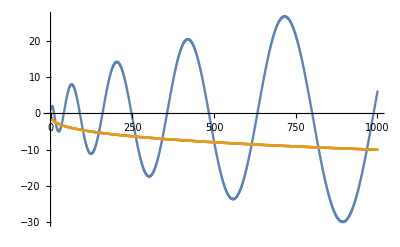

```mathematica
ListPlot[{Re[flist],Im[flist]}]
```

According to the above definitions, the list of the DFT numbers is

```mathematica
hnumbers[n_]:=1/Sqrt[Num]Sum[flist[[k+1]]Exp[2Pi I k n/Num],{k,0,Num-1}]
```

```mathematica
hlist=Table[hnumbers[n],{n,0,Num-1}];
```

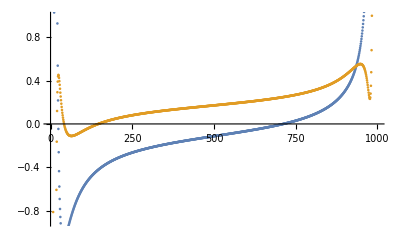

```mathematica
ListPlot[{Re[hlist],Im[hlist]}]
```

```mathematica
Timing[Table[hnumbers[n],{n,0,Num-1}]][[1]]
```

11.8973

Exercise: The Timing command returns the time (in seconds) to evaluate an expression. In the example given, above explore how the time resources vary as a function of the size, Num, of the list.

```mathematica
?Timing
```

Timing[expr] evaluates expr, and returns a list of the time in seconds used, together with the result obtained.

### Mathematica's FFT function

In the above exercise you might have noticed how time time resources scale the square power of  Num.
The Fast Fourier Transform algorithm has superior scaling properties, and is implemented by the Mathematica function

```mathematica
?Fourier
```

Fourier[list] finds the discrete Fourier transform of a list of complex numbers.
Fourier[list,{p_1,p_2,…}] returns the specified positions of the discrete Fourier transform.

```mathematica
FFThlist=Fourier[flist];
```

```mathematica
ListPlot[{Re[FFThlist],Im[FFThlist]}]
```

-Graphics-

and which agrees with the result obtained above, but whose evaluation time is dramatically improved from the latter.

```mathematica
Timing[Fourier[flist]][[1]]
```

0.000098